```mathematica
s = 0.006529828886969226
```

0.00652983

```mathematica
edistNorm = NormalDistribution[-0.00011849766017034486,0.004097422554612836]
```

NormalDistribution[-0.000118498,0.00409742]

```mathematica
(* 10 m distribution for USDC-ETH *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandle = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044,0.0015427669619594313]
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
edistWethUsdc90dFiltered1hCandle = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044*6,0.0015427669619594313*(6/1.4646547203677354)^(1/1.4646547203677354)]
```

StableDistribution[1,1.46465,-0.0496207,-0.0000633183,0.00404045]

```mathematica
(* Great *)
(* Now be super rigorous w it! *)
```

```mathematica
CDF[StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044,0.0015427669619594313],3]
```

0.999997

```mathematica
InverseCDF[edistWethUsdc90dFiltered10MinCandle, 0.99]
```

0.0124991

```mathematica
mu = -0.00011849766017034486
```

-0.000118498

```mathematica
sig= 0.004097422554612836
```

0.00409742

```mathematica
CDF[NormalDistribution[0,1], 0]
```

1/2

```mathematica
CDF[NormalDistribution[0,1], -sig]
```

0.498365

```mathematica
(1-CDF[NormalDistribution[0,1], -sig])/(1-CDF[NormalDistribution[0,1], 0])
```

1.00327

```mathematica
Log[1.003269261047541]
```

0.00326393

```mathematica
0.0032639286325196527+sig^2/2.0
```

0.00327232

```mathematica
(* Perfect .... this is > 0 so can use l * Q to make this go to 0 *)
```

```mathematica
mu
```

-0.000118498

```mathematica
(* Bring in mu *)
```

```mathematica
CDF[NormalDistribution[0,1], -(mu-2*s)/sig-sig]
```

0.999341

```mathematica
1-CDF[NormalDistribution[mu - 2*s, sig],0]
```

0.000649488

```mathematica
CDF[NormalDistribution[mu - 2*s, sig],0]
```

0.999351

```mathematica
CDF[NormalDistribution[0,1], -(mu-2*s)/sig]
```

0.999351

```mathematica
(1-CDF[NormalDistribution[0,1], -(mu-2*s)/sig-sig])/(1-CDF[NormalDistribution[0,1], -(mu-2*s)/sig])
```

1.01437

```mathematica
(* even better! Beautiful :) ... mu + sig^2/2 - l * Q + Log[(1-CDF)/(1-CDF)] ≤ 0 to have negative EV at Q *)
```

```mathematica
Exp[mu + sig^2/2.0]
```

0.99989

```mathematica
mu + sig^2/2.0
```

-0.000110103

```mathematica
2*s
```

0.0130597

```mathematica
rhs = mu-2*s  + sig^2/2.0 + Log[(1-CDF[NormalDistribution[0,1], -(mu-2*s)/sig-sig])/(1-CDF[NormalDistribution[0,1], -(mu-2*s)/sig])]
```

0.00110089

```mathematica
(* What's the expected PnL given > s when lambda = 0? *)
```

```mathematica
Exp[rhs]-1
```

0.0011015

```mathematica
(* 0.11% in 10m interval as scalp is pretty small already. Now, ensure we make that EV ≤ 0 ... *)
```

```mathematica
(* need l*Q ≥ rhs for negative EV. Take l'*(Q/Qmax) ≥ rhs ... l' ≥ rhs * (Qmax/Q) *)
```

```mathematica
(* if take l' = rhs * (Qmax/Q0), know that EV < 0 whenever Q > Q0 *)
```

```mathematica
lNormUsdcWethPrime[q_] := (1/q) * rhs
```

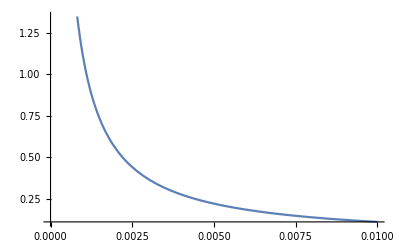

```mathematica
Plot[lNormUsdcWethPrime[q], {q, 0, 0.01}]
```

```mathematica
Exp[1.5]
```

4.48169

```mathematica
Exp[-1.5]
```

0.22313

```mathematica
(* Check norm EV values given Q0 choice *)
```

```mathematica
evNormUsdcWeth[qp_, q_]:= q*(Exp[rhs - lNormUsdcWethPrime[qp]*q]-1)
```

```mathematica
Manipulate[Plot[evNormUsdcWeth[qp, q], {q, 0, 1}], {qp, 0.00025, 0.01}]
```

```mathematica
(* Zoom in around 1% mark ... *)
```

```mathematica
Manipulate[Plot[evNormUsdcWeth[qp, q], {q, 0, 0.005}], {qp, 0.00025, 0.01}]
```

```mathematica
(* EV of < 0.01 bps of OI max/cap on scalp if take lprime to happen at Q = 1% of cap *)
```

```mathematica
(* Take 0.1% of cap as the l anchor *)
```

```mathematica
lNormUsdcWethPrime[0.001]
```

1.10089

```mathematica
Exp[lNormUsdcWethPrime[0.001]]
```

3.00685

```mathematica
Exp[-lNormUsdcWethPrime[0.001]]
```

0.332573

```mathematica
(* if take up 100% of cap, will have 4x slippage to upside and -76% slippage to downside *)
```

```mathematica
(* What's the slippage function? Compare vs Uniswap as well ... *)
```

```mathematica
(* Us: P/P0 - 1 = e^{s+l*q} - 1; Uniswap: P/P0 - 1 = (1+q)^2 - 1 *)
```

```mathematica
(* take s = 0 for here *)
```

```mathematica
slippageNormUsdcsWeth[qp_, q_]:= Exp[lNormUsdcWethPrime[qp]*q] - 1
```

```mathematica
slippageNormWithSpreadUsdcsWeth[qp_, q_]:= Exp[s*Sign[q]+lNormUsdcWethPrime[qp]*q] - 1
```

```mathematica
uniswapSlippageUp[q_] := (1+q)^2 - 1
```

```mathematica
uniswapSlippageDown[q_]:= 1/(1+q)^2 - 1
```

```mathematica
Manipulate[Plot[slippageNormUsdcsWeth[qp, q], {q, 0, 1}, PlotRange->All], {qp, 0.00025, 0.01}]
```

```mathematica
Manipulate[Plot[{slippageNormUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 1.0}], {qp, 0.00025, 0.01}]
```

```mathematica
(* Values that matter for us: q in [0, 1] where q is percentage of OI cap user takes up *)
```

```mathematica
(* For values that matter, can calibrate slippage such that scalp trade is -EV for traders taking up > 0.1% of cap when price jumps *)
```

```mathematica
(* We are the blue. Uniswap V2 x*y=k is the orange in the same region. We can have less slippage than Uniswap in all regions of interest. Chart above assumes our OI max is the same as 1/2 entire Uniswap liquidity (# of 'x' tokens in pool) *)
```

```mathematica
(* Compare with the static spread as well ... *)
```

```mathematica
Manipulate[Plot[{slippageNormWithSpreadUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 1.0}], {qp, 0.00025, 0.01}]
```

```mathematica
Manipulate[Plot[{slippageNormWithSpreadUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 0.2}], {qp, 0.00025, 0.01}]
```

```mathematica
(* Still beautiful. Zoom in around x = 0 *)
```

```mathematica
Manipulate[Plot[{slippageNormWithSpreadUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 0.01}], {qp, 0.00025, 0.01}]
```

```mathematica
(* And the static spread is apparent :) *)
```

```mathematica
(* What about slippage on the downside? *)
```

```mathematica
Manipulate[Plot[{slippageNormWithSpreadUsdcsWeth[qp, -x], uniswapSlippageDown[x] }, {x, 0, 1.0}], {qp, 0.00025, 0.01}]
```

```mathematica
(* Beautiful here as well ... *)
```

```mathematica
Manipulate[Plot[{slippageNormWithSpreadUsdcsWeth[qp, -x], uniswapSlippageDown[x] }, {x, 0, 0.1}], {qp, 0.00025, 0.01}]
```

```mathematica
(* Now: 1. check w stable distribution math + caps; 2. Can a user profitably chunk the trade over the next 40 blocks to get EV ≥ 0? *)
```

```mathematica
(* From Mathematica fit ... *)
```

```mathematica
edistWethUsdc90dFiltered10MinCandle
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
cp = 4
```

4

```mathematica
Log[1.0+cp]
```

1.60944

```mathematica
s
```

0.00652983

```mathematica
edistWethUsdcYv10MinCandle = StableDistribution[1,1.4646547203677354,-0.04962071457296463,-0.000010553047315527044-2.0*s,0.0015427669619594313]
```

StableDistribution[1,1.46465,-0.0496207,-0.0130702,0.00154277]

```mathematica
1+cp
```

5

```mathematica
gInv = Log[1.0+cp]
```

1.60944

```mathematica
1-CDF[edistWethUsdcYv10MinCandle, 0]
```

0.00933603

```mathematica
CDF[edistWethUsdcYv10MinCandle, 0]
```

0.990664

```mathematica
(* Beautiful.... Less than normal *)
```

```mathematica
1-CDF[edistWethUsdcYv10MinCandle, gInv]
```

7.48682×10^-6

```mathematica
CDF[edistWethUsdcYv10MinCandle, gInv]
```

0.999993

```mathematica
(* This is to reach the 5x in 10m so negligible which is good *)
```

```mathematica
1-CDF[edistWethUsdcYv10MinCandle, 0]-(1+cp)*(1-CDF[edistWethUsdcYv10MinCandle, gInv])
```

0.0092986

```mathematica
NIntegrate[PDF[edistWethUsdcYv10MinCandle, y]*Exp[y], {y, 0, gInv}]
```

0.00956781

```mathematica
(NIntegrate[PDF[edistWethUsdcYv10MinCandle, y]*Exp[y], {y, 0, gInv}])/(1-CDF[edistWethUsdcYv10MinCandle, 0]-(1+cp)*(1-CDF[edistWethUsdcYv10MinCandle, gInv]))
```

1.02895

```mathematica
logStableUsdcWeth = Log[(NIntegrate[PDF[edistWethUsdcYv10MinCandle, y]*Exp[y], {y, 0, gInv}])/(1-CDF[edistWethUsdcYv10MinCandle, 0]-(1+cp)*(1-CDF[edistWethUsdcYv10MinCandle, gInv]))]
```

0.0285405

```mathematica
rhs
```

0.00110089

```mathematica
(* way higher than EV from norm :)... 2.854% for stable vs 0.11% for norm *)
```

```mathematica
lStableUsdcWethPrime[q_] := (1/q) * logStableUsdcWeth
```

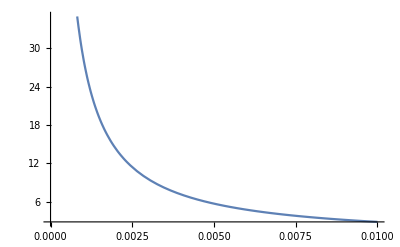

```mathematica
Plot[lStableUsdcWethPrime[q], {q, 0, 0.01}]
```

```mathematica
(* Compare with normal ... *)
```

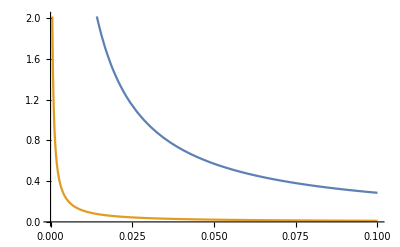

```mathematica
Plot[{lStableUsdcWethPrime[q], lNormUsdcWethPrime[q]}, {q, 0, 0.1}]
```

```mathematica
lStableUsdcWethPrime[0.01]
```

2.85405

```mathematica
lNormUsdcWethPrime[0.01]
```

0.110089

```mathematica
lStableUsdcWethPrime[0.01]/lNormUsdcWethPrime[0.01]-1
```

24.9248

```mathematica
(* 25x difference! in market impact parameter to obtain negative EV for 1% of OI cap *)
```

```mathematica
(* 1% of OI for negative EV is likely what we want. Check slippage! *)
```

```mathematica
Exp[lNormUsdcWethPrime[0.01]]
```

1.11638

```mathematica
Exp[lStableUsdcWethPrime[0.01]]
```

17.3579

```mathematica
Exp[-lStableUsdcWethPrime[0.01]]
```

0.0576105

```mathematica
slippageStableUsdcsWeth[qp_, q_]:= Exp[lStableUsdcWethPrime[qp]*q] - 1
```

```mathematica
slippageStableWithSpreadUsdcsWeth[qp_, q_]:= Exp[s*Sign[q]+lStableUsdcWethPrime[qp]*q] - 1
```

```mathematica
Manipulate[Plot[slippageStableUsdcsWeth[qp, q], {q, 0, 1}, PlotRange->All], {qp, 0.0025, 0.1}]
```

```mathematica
(* Zoom in for smaller fish trades ... *)
```

```mathematica
Manipulate[Plot[slippageStableUsdcsWeth[qp, q], {q, 0, 0.1}, PlotRange->All], {qp, 0.0025, 0.1}]
```

```mathematica
(* Compare w Uniswap ... *)
```

```mathematica
Manipulate[Plot[{slippageStableUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 1.0}], {qp, 0.0025, 0.1}]
```

```mathematica
(* Zoom in for small fish *)
```

```mathematica
Manipulate[Plot[{slippageStableUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 0.25}], {qp, 0.0025, 0.1}]
```

```mathematica
(* If we risk 2% of the OI cap vs 1%, we're at Uniswap slippage levels. This is beautiful *)
```

```mathematica
(* Plot with static spread then check how much we can get milked for <= 2% (worst case) ... max of EV given Q0 = 2% of Qmax .. *)
```

```mathematica
Manipulate[Plot[{slippageStableWithSpreadUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 1.0}], {qp, 0.0025, 0.1}]
```

```mathematica
Manipulate[Plot[{slippageStableWithSpreadUsdcsWeth[qp, x], uniswapSlippageUp[x] }, {x, 0, 0.25}], {qp, 0.0025, 0.1}]
```

```mathematica
(* And on the downside ... *)
```

```mathematica
Manipulate[Plot[{slippageStableWithSpreadUsdcsWeth[qp, -x], uniswapSlippageDown[x] }, {x, 0, 1.0}], {qp, 0.0025, 0.1}]
```

```mathematica
h = Log[NIntegrate[PDF[edistWethUsdcYv10MinCandle, y]*Exp[y], {y, 0, gInv}]/(1-CDF[edistWethUsdcYv10MinCandle,0])]
```

0.0245228

```mathematica
rho = (1+cp)*(1-CDF[edistWethUsdcYv10MinCandle,gInv])/(1-CDF[edistWethUsdcYv10MinCandle,0])
```

0.00400964

```mathematica
evStableUsdcWeth[qp_, q_]:= q*(Exp[h - lStableUsdcWethPrime[qp]*q]-1+rho)
```

```mathematica
Manipulate[Plot[evStableUsdcWeth[qp, q], {q, 0, 1}], {qp, 0.0025, 0.1}]
```

```mathematica
(* Zoom in where it really counts ... *)
```

```mathematica
Manipulate[Plot[evStableUsdcWeth[qp, q], {q, 0, 0.05}], {qp, 0.0025, 0.1}]
```

```mathematica
(* EV max happens at 1/2 of Q0 (same as norm). And for that 1% size on the 2% EV setting, milk the system for about 0.000143 * OI cap => 1.43 bps of OI cap on the scalp *)
```

```mathematica
evStableUsdcWeth[0.02, 0.01]
```

0.000143149

```mathematica
(* so for example, if the cap is 100M, we'd expect to get milked for max $14.3k on the scalp with size $1M. *)
```

```mathematica
0.000143*100000000
```

14300.

```mathematica
(* Since fees are about 15bps on each side => so 30 bps total. Eats into ~20% of scalps profit ... *)
```

```mathematica
0.0030 * 1000000
```

3000.

```mathematica
3000/14300.0
```

0.20979

```mathematica
(* How much more volume does it take to overcome that scalp if charging 30bps? *)
```

```mathematica
14300 - 3000.0
```

11300.

```mathematica
11300/(0.0030)
```

3.76667×10^6

```mathematica
(* $3.76M more in volume needed to recover on $1M scalp with $100M cap. Numbers scale accordingly. If we have caps at $100M OI, then likely doing way more than $3.76M in volume per day. Profitable scalp also happens only ~1% of the time, if fit params correctly *)
```

```mathematica
(* More realistically at launch, $10M OI cap, means $100k position size scalp with $1.4k in profit, 1% of the time. Need volume of $376k to recover those funds, which is fine *)
```